```mathematica
Clear[k,b,mL,mm,Flim,t,xm0,dxm0,xL0,dxL0]
```

```mathematica
Subscript[x, L] stuff
```

```mathematica
FullSimplify[InverseLaplaceTransform[(Flim  k)/(ml mm s^5+mm k s^3+ml k s^3),s,t],{k>0,Flim>0,mm>0,ml>0}]
```

(Flim (-2 ml mm+k (ml+mm) t^2+2 ml mm Cos[√(k (1/ml+1/mm)) t]))/(2 k (ml+mm)^2)

```mathematica
Simplify[InverseLaplaceTransform[(mm xm0 k)/(ml mm s^3+mm k s+ml k s),s,t]]
```

-(ⅇ^(-(√(-k (ml+mm)) t)/(√ml √mm)) (-1+ⅇ^((√(-k (ml+mm)) t)/(√ml √mm)))^2 mm xm0)/(2 (ml+mm))

```mathematica
InverseLaplaceTransform[(mm dxm0 k)/(ml mm s^4+mm k s^2+ml k s^2),s,t]
```

dxm0 k mm (-(ⅇ^(-(√(-k (ml+mm)) t)/(√ml √mm)) (-1+ⅇ^((2 √(-k (ml+mm)) t)/(√ml √mm))) √ml √mm)/(2 k (ml+mm) √(-k (ml+mm)))+t/(k (ml+mm)))

```mathematica
Simplify[InverseLaplaceTransform[(ml mm xl0 s)/(ml mm s^2+mm k +ml k),s,t]]
```

1/2 ⅇ^(-(√(-k (ml+mm)) t)/(√ml √mm)) (1+ⅇ^((2 √(-k (ml+mm)) t)/(√ml √mm))) xl0

```mathematica
FullSimplify[InverseLaplaceTransform[(ml mm dxl0)/(ml mm s^2+mm k +ml k),s,t],{k>0,Flim>0,mm>0,ml>0}]
```

(dxl0 ml mm Sin[√(k (1/ml+1/mm)) t])/(√(k ml mm (ml+mm)))

```mathematica
Simplify[InverseLaplaceTransform[(ml xl0 k)/(ml mm s^3+mm k s +ml k s),s,t]]
```

-(ⅇ^(-(√(-k (ml+mm)) t)/(√ml √mm)) (-1+ⅇ^((√(-k (ml+mm)) t)/(√ml √mm)))^2 ml xl0)/(2 (ml+mm))

```mathematica
FullSimplify[InverseLaplaceTransform[(ml dxl0 k)/(ml mm s^4+mm k s^2 +ml k s^2),s,t],{k>0,Flim>0,mm>0,ml>0}]
```

(dxl0 ml (t-(ml mm Sin[√(k (1/ml+1/mm)) t])/(√(k ml mm (ml+mm)))))/(ml+mm)

```mathematica
FullSimplify[InverseLaplaceTransform[(Flim  k)/(ml mm s^5+mm k s^3+ml k s^3),s,t]+InverseLaplaceTransform[(mm xm0 k)/(ml mm s^3+mm k s+ml k s),s,t]+InverseLaplaceTransform[(mm dxm0 k)/(ml mm s^4+mm k s^2+ml k s^2),s,t]+InverseLaplaceTransform[(ml mm xl0 s)/(ml mm s^2+mm k +ml k),s,t]+InverseLaplaceTransform[(ml mm dxl0)/(ml mm s^2+mm k +ml k),s,t]+InverseLaplaceTransform[(ml xl0 k)/(ml mm s^3+mm k s +ml k s),s,t]+InverseLaplaceTransform[(ml dxl0 k)/(ml mm s^4+mm k s^2 +ml k s^2),s,t],{k>0,mm>0,ml>0}]
```

-1/(2 k^(3/2) (ml+mm)^(5/2))ⅈ ⅇ^(-ⅈ √(k (1/ml+1/mm)) t) (-dxm0 k (-(ml mm)^(3/2)+ⅇ^(2 ⅈ √(k (1/ml+1/mm)) t) (ml mm)^(3/2)-√(ml mm^5)+ⅇ^(2 ⅈ √(k (1/ml+1/mm)) t) √(ml mm^5)-2 ⅇ^(√(-(k (ml+mm))/(ml mm)) t) ml mm √(-k (ml+mm)) t-2 ⅇ^(√(-(k (ml+mm))/(ml mm)) t) mm^2 √(-k (ml+mm)) t)+dxl0 k ((-1+ⅇ^(2 ⅈ √(k (1/ml+1/mm)) t)) √(ml mm^5)+2 ⅇ^(√(-(k (ml+mm))/(ml mm)) t) ml^2 √(-k (ml+mm)) t+ml mm (-√(ml mm)+ⅇ^(2 ⅈ √(k (1/ml+1/mm)) t) √(ml mm)+2 ⅇ^(√(-(k (ml+mm))/(ml mm)) t) √(-k (ml+mm)) t))+√(-k (ml+mm)) (mm ((-1+ⅇ^(ⅈ √(k (1/ml+1/mm)) t))^2 Flim ml+(1+ⅇ^(2 ⅈ √(k (1/ml+1/mm)) t)) k (ml+mm) (xl0-xm0))+ⅇ^(√(-(k (ml+mm))/(ml mm)) t) k (ml+mm) (Flim t^2+2 ml xl0+2 mm xm0)))

```mathematica
Subscript[x, m] Stuff
```

```mathematica
FullSimplify[InverseLaplaceTransform[Flim/(s (mm s^2+k-k^2/(ml s^2+k))),s,t],{k>0,Flim>0,mm>0,ml>0}]
```

(Flim (2 ml^2+k (ml+mm) t^2-2 ml^2 Cos[√(k (1/ml+1/mm)) t]))/(2 k (ml+mm)^2)

```mathematica
InverseLaplaceTransform[(ml xl0 k s)/((ml s^2+k)(mm s^2+k)-k^2),s,t]
```

-(ⅇ^(-(√(-k (ml+mm)) t)/(√ml √mm)) (-1+ⅇ^((√(-k (ml+mm)) t)/(√ml √mm)))^2 ml xl0)/(2 (ml+mm))

```mathematica
FullSimplify[InverseLaplaceTransform[(ml dxl0 k)/((ml s^2+k)(mm s^2+k)-k^2),s,t],{k>0,Flim>0,mm>0,ml>0}]
```

(dxl0 ml (t-(ml mm Sin[√(k (1/ml+1/mm)) t])/(√(k ml mm (ml+mm)))))/(ml+mm)

```mathematica
InverseLaplaceTransform[(mm xm0 s)/(mm s^2+k-k^2/(ml s^2+k)),s,t]
```

mm (1/(ml+mm)+(ⅇ^(-(√(-k (ml+mm)) t)/(√ml √mm)) (1+ⅇ^((2 √(-k (ml+mm)) t)/(√ml √mm))) ml)/(2 mm (ml+mm))) xm0

```mathematica
InverseLaplaceTransform[(mm dxm0)/(mm s^2+k-k^2/(ml s^2+k)),s,t]
```

dxm0 mm ((ⅇ^(-(√(-k (ml+mm)) t)/(√ml √mm)) (-1+ⅇ^((2 √(-k (ml+mm)) t)/(√ml √mm))) ml^(3/2))/(2 √mm (ml+mm) √(-k (ml+mm)))+t/(ml+mm))

```mathematica
d/dt Subscript[x, L] stuff:
```

```mathematica
xL[t_] :=-(Flim mL mm)/(k(mL+mm)^2)+(Flim t^2)/(2(mL+mm))+(Flim mL mm Cos[t √(k(1/mL+1/mm))])/(k(mL+mm)^2)+(dxL0 mL mm Sin[t √(k(1/mL+1/mm))])/(√(k mL mm(mL+mm)))+(dxL0 mL t)/(mL+mm)-(dxL0 mL^2 mm Sin[t √(k(1/mL+1/mm))])/((mL+mm)√(k mL mm(mL+mm)))
```

```mathematica
xL'[t]
```

(dxL0 mL)/(mL+mm)+(Flim t)/(mL+mm)+(dxL0 mL √(k (1/mL+1/mm)) mm Cos[√(k (1/mL+1/mm)) t])/(√(k mL mm (mL+mm)))-(dxL0 mL^2 √(k (1/mL+1/mm)) mm Cos[√(k (1/mL+1/mm)) t])/((mL+mm) √(k mL mm (mL+mm)))-(Flim mL √(k (1/mL+1/mm)) mm Sin[√(k (1/mL+1/mm)) t])/(k (mL+mm)^2)

```mathematica
FullSimplify[Solve[0==xL''[t],t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0},{t→-ArcCos[-1+(2 Flim^2 mL)/(Flim^2 mL+dxL0^2 k mm (mL+mm))]/(√(k (1/mL+1/mm)))},{t→ArcCos[-1+(2 Flim^2 mL)/(Flim^2 mL+dxL0^2 k mm (mL+mm))]/(√(k (1/mL+1/mm)))}}

```mathematica
Solve[0==FullSimplify[xL'[ArcCos[-1+(2 Flim^2 mL)/(Flim^2 mL+dxL0^2 k mm (mL+mm))]/(√(k (1/mL+1/mm)))]],dxL0]
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve[0==(dxL0 mL)/(mL+mm)-(2 Flim √((dxL0^2 Flim^2 k mL mm (mL+mm))/((Flim^2 mL+dxL0^2 k mm (mL+mm))^2)))/(√(k (1/mL+1/mm)) (mL+mm))-(dxL0 k mL^3 √(k (1/mL+1/mm)) mm^2 (-1+(2 Flim^2 mL)/(Flim^2 mL+dxL0^2 k mm (mL+mm))))/(k mL mm (mL+mm))^(3/2)+(dxL0 mL √(k (1/mL+1/mm)) mm (-1+(2 Flim^2 mL)/(Flim^2 mL+dxL0^2 k mm (mL+mm))))/(√(k mL mm (mL+mm)))+(Flim ArcCos[-1+(2 Flim^2 mL)/(Flim^2 mL+dxL0^2 k mm (mL+mm))])/(√(k (1/mL+1/mm)) (mL+mm)),dxL0]

```mathematica
Clear[k,b,mL,mm,Flim,t,xm0,dxm0,xL0,dxL0,t]
```

```mathematica
(*dxL0=-10;*)
Flim=-1000;

mm=3;
mL=1;

k=5000;
```

```mathematica
FindRoot[xL'[ArcCos[-1+(2 Flim^2 mL)/(Flim^2 mL+dxL0^2 k mm (mL+mm))]/(√(k (1/mL+1/mm)))]==0,{dxL0,-0.01,-100}]
```

{dxL0→-16.218}

```mathematica
d/dt Subscript[F, L] stuff:
```

```mathematica
F[t_] := (Flim mL^2)/(mL+mm)^2+(Flim mL mm)/(mL+mm)^2-(Flim mL^2 Cos[t √(k(1/mL+1/mm))])/(mL+mm)^2-(Flim mL mm Cos[t √(k(1/mL+1/mm))])/(mL+mm)^2-(dxL0 mL mm k Sin[t √(k(1/mL+1/mm))])/(√(k mL mm (mL+mm)))
```

```mathematica
FullSimplify[F[t]]
```

(Flim mL-Flim mL Cos[√(k (1/mL+1/mm)) t]-dxL0 √(k mL mm (mL+mm)) Sin[√(k (1/mL+1/mm)) t])/(mL+mm)

```mathematica
FullSimplify[F'[t]]
```

(√(k (1/mL+1/mm)) (-dxL0 √(k mL mm (mL+mm)) Cos[√(k (1/mL+1/mm)) t]+Flim mL Sin[√(k (1/mL+1/mm)) t]))/(mL+mm)

```mathematica
Solve[0==F'[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-(mL √(k/mL+k/mm) mm ArcCos[-(Flim √mL)/(√(Flim^2 mL+dxL0^2 k mL mm+dxL0^2 k mm^2))])/(k (mL+mm))},{t→(mL √(k/mL+k/mm) mm ArcCos[-(Flim √mL)/(√(Flim^2 mL+dxL0^2 k mL mm+dxL0^2 k mm^2))])/(k (mL+mm))},{t→-(mL √(k/mL+k/mm) mm ArcCos[(Flim √mL)/(√(Flim^2 mL+dxL0^2 k mL mm+dxL0^2 k mm^2))])/(k (mL+mm))},{t→(mL √(k/mL+k/mm) mm ArcCos[(Flim √mL)/(√(Flim^2 mL+dxL0^2 k mL mm+dxL0^2 k mm^2))])/(k (mL+mm))}}

```mathematica
FullSimplify[Solve[0==F'[t],t],{k>0,mm>0,ml>0}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-ArcCos[-(Flim √mL)/(√(Flim^2 mL+dxL0^2 k mm (mL+mm)))]/(√(k (1/mL+1/mm)))},{t→ArcCos[-(Flim √mL)/(√(Flim^2 mL+dxL0^2 k mm (mL+mm)))]/(√(k (1/mL+1/mm)))},{t→-ArcCos[(Flim √mL)/(√(Flim^2 mL+dxL0^2 k mm (mL+mm)))]/(√(k (1/mL+1/mm)))},{t→ArcCos[(Flim √mL)/(√(Flim^2 mL+dxL0^2 k mm (mL+mm)))]/(√(k (1/mL+1/mm)))}}

```mathematica
FullSimplify[F[ArcCos[-(Flim √mL)/(√(Flim^2 mL+dxL0^2 k mm (mL+mm)))]/(√(k (1/mL+1/mm)))],{k>0,mm>0,ml>0}]
```

(Flim mL-dxL0 k mm √(mL (mL+mm)) √((dxL0^2 (mL+mm))/(Flim^2 mL+dxL0^2 k mm (mL+mm)))+(Flim^2 mL^(3/2))/(√(Flim^2 mL+dxL0^2 k mm (mL+mm))))/(mL+mm)

```mathematica
{{}, {}}
```

```mathematica
Solve[0==(ⅇ^(ⅈ t)-ⅇ^(-ⅈ t))/(2 ⅈ)-t/10 ,t]
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve[0==-1/2 ⅈ (-ⅇ^(-ⅈ t)+ⅇ^(ⅈ t))-t/10,t]

```mathematica
Solve[0==Sin[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0}}

```mathematica
f[t_]:=Sin[t]-t/b-a
```

```mathematica
f'[t]
```

-1/b+Cos[t]

True

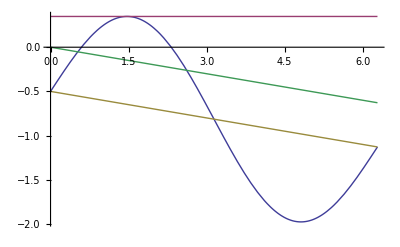

```mathematica
b=10;
a=.5;
f[ArcCos[1/b]]≥0
Plot[{f[t],f[ArcCos[1/b]],-t/b-a,-t/b},{t,0,2π}]
```

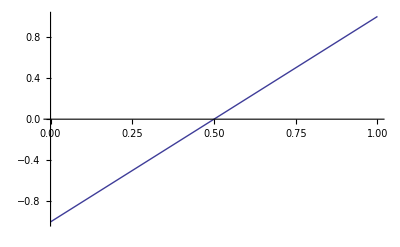

```mathematica
Plot[{2 x-1},{x,0,1}]
```

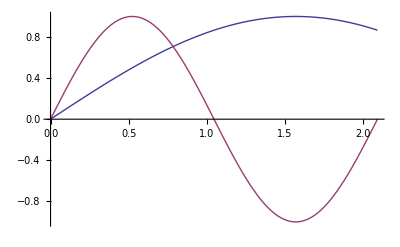

```mathematica
Plot[{Sin[t],Sin[3 t]},{t,0,2 π/3}]
```